# Maly projekt 3 - Boole

## Jan Czechowski

## zad 1.

```mathematica
wyrazenie1=((A&&B)||!C)&&(!B||(C&&!A))||(!A&&!B&&!C)
Boole[BooleanTable[wyrazenie1,{A,B,C}]]
```

(((A&&B)||!C)&&(!B||(C&&!A)))||(!A&&!B&&!C)

{0,0,0,1,0,0,0,1}

## zad 2.

```mathematica
wyrazenieBoolowskie=BooleanFunction[{0,1,0,0,0,0,1,0},{A,B,C}]
```

(A&&B&&!C)||(!A&&!B&&C)

## zad 3.

## zad 4.

```mathematica
BooleanConvert[((A&&B)||!C)&&(!B||(C&&!A))||(!A&&!B&&!C),"DNF"]
```

!B&&!C

## zad 5.

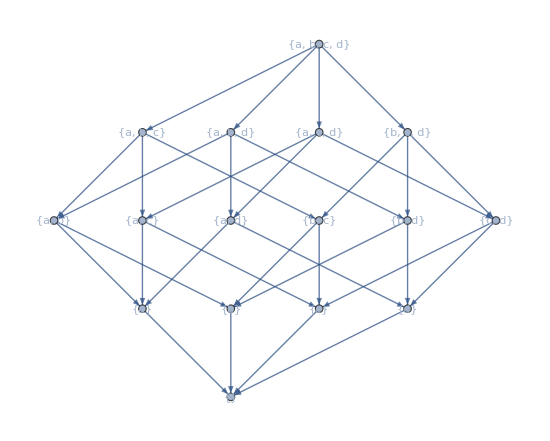

```mathematica
X={a,b,c,d};

subsets=Subsets[X];
subsetLabels=Map[Function[s,"{"<>StringJoin[Riffle[Map[ToString,s],", "]]<>"}"],subsets];
subsetToLabel=AssociationThread[subsets,subsetLabels];
edgesAll=Flatten[Table[s1=subsets[[i]];
s2=subsets[[j]];
If[SubsetQ[s1,s2]&&s1=!=s2,subsetToLabel[s1]->subsetToLabel[s2],Nothing],{i,Length[subsets]},{j,Length[subsets]}],1];

(*Usuwamy duplikaty*)
edgesAll=DeleteDuplicates[edgesAll];
gAll=Graph[edgesAll,VertexLabels->"Name",DirectedEdges->True];
hasse=TransitiveReductionGraph[gAll,VertexLabels->Placed["Name",Center],GraphLayout->"LayeredDigraphEmbedding",DirectedEdges->False];
hasse
```